```mathematica
len=100;
NTrajs=10^4;
diffD=0.9;(*um^2/s*)
dt=0.05;(*s*)
```

```mathematica
sigma=Sqrt[2*diffD*dt]
```

0.3

```mathematica
For[j=2,j≤ len,j++,
rx=RandomVariate[NormalDistribution[0,sigma]];
Trajs[[1,j,1]]=Trajs[[1,j-1,1]]+rx;
ry=RandomVariate[NormalDistribution[0,sigma]];
Trajs[[1,j,2]]=Trajs[[1,j-1,2]]+ry;
];
```

```mathematica
Trajs[[1,All,1]]=MapThread[Plus, {Trajs[[1,All,1]], randomx}]
```

{-0.0131722,0.14714,-0.0102128,0.148629,0.153987,0.270506,0.425901,0.405511,0.322873,0.352666,0.366475,0.200216,0.455026,0.520777,0.711128,0.799678,0.930816,0.840041,0.642485,0.418667,0.455237,0.54724,0.612151,0.627423,0.422028,0.240227,0.29838,0.283775,0.509876,0.609136,0.560753,1.00176,0.989929,0.958188,0.756653,0.716861,0.617987,0.636836,0.733903,0.905978,1.01981,1.09819,0.944342,0.818809,0.844593,0.819665,0.966529,1.03859,1.16927,0.967964,0.825631,0.71742,0.663194,0.644687,0.843045,0.703374,0.865325,1.16552,1.06778,1.22486,1.17931,1.05804,1.07841,1.17565,1.1027,1.03797,1.21958,1.10377,1.12805,1.26865,1.23083,1.1516,0.982659,0.905719,1.16006,1.33218,1.50639,1.38979,1.43963,1.51324,1.32812,1.14189,1.2115,1.34863,1.24347,1.03824,0.960913,0.96209,0.970876,0.806184,0.958139,1.04942,1.00125,1.0168,1.0954,0.976103,0.911681,0.897669,0.702382,0.819803}

#### Brownian

```mathematica
NTrajs=10^4;
```

```mathematica
Trajs=Table[{0.0,0.0},{NTrajs},{len}];
```

```mathematica
For[i=1,i≤ NTrajs,i++,
For[j=2,j≤ len,j++,
rx=RandomVariate[NormalDistribution[0,sigma]];
Trajs[[i,j,1]]=Trajs[[i,j-1,1]]+rx;
ry=RandomVariate[NormalDistribution[0,sigma]];
Trajs[[i,j,2]]=Trajs[[i,j-1,2]]+ry;
];
randomx = RandomVariate[NormalDistribution[0,sigma/10],100];
randomy = RandomVariate[NormalDistribution[0,sigma/10],100];
Trajs[[i,All,1]]=MapThread[Plus, {Trajs[[i,All,1]], randomx}];
Trajs[[i,All,2]]=MapThread[Plus, {Trajs[[i,All,2]], randomy}];
]
```

```mathematica
For[i=1,i≤ NTrajs,i++,
For[j=2,j≤ len,j++,
rr=RandomVariate[RayleighDistribution[sigma]];
theta=RandomReal[{0,2 Pi}];
rx=rr*Cos[theta];
ry=rr*Sin[theta];
Trajs[[i,j,1]]=Trajs[[i,j-1,1]]+rx;
Trajs[[i,j,2]]=Trajs[[i,j-1,2]]+ry;
]
]
```

```mathematica
Export["E:\\KG\\Trajs\\BW\\trajs.csv",N[Trajs]]
```

E:\KG\Trajs\BW\trajs.csv

```mathematica
ObjectTrajs=Import["E:\\KG\\Trajs\\BW\\trajs.csv"];
```

```mathematica
Length[ObjectTrajs[[1]]]
```

500

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\BW\\trajs_ray.dat"];
```

```mathematica
ObjectTrajs2=Get["E:\\KG\\Trajs\\BW\\trajs.dat"];
```

```mathematica
Export["E:\\KG\\Trajs\\BW\\BW.json",N[Trajs],"JSON"]
```

E:\KG\Trajs\BW\BW.json

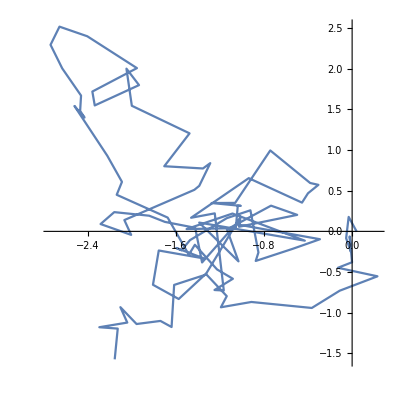

```mathematica
ListLinePlot[Trajs[[10000]],AspectRatio->1,PlotRange->All]
```

#### Directed motion

```mathematica
NTrajs=1000;
```

```mathematica
Trajs=Table[{0.0,0.0},{NTrajs},{len}];
```

```mathematica
For[i=1,i≤ NTrajs,i++,
R=RandomReal[{2,100}];
beta=RandomReal[{0,2 Pi}];
velo=Sqrt[4*diffD*R/(dt*len)];
For[j=2,j≤ len,j++,
rr=RandomVariate[RayleighDistribution[sigma]];
theta=RandomReal[{0,2 Pi}];
rx=rr*Cos[theta]+velo*dt*Cos[beta];
ry=rr*Sin[theta]+velo*dt*Sin[beta];
Trajs[[i,j,1]]=Trajs[[i,j-1,1]]+rx;
Trajs[[i,j,2]]=Trajs[[i,j-1,2]]+ry;
]
]
```

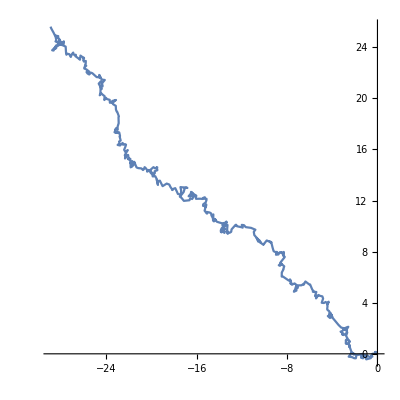

```mathematica
ListLinePlot[Trajs[[1]],AspectRatio->1,PlotRange->All]
```

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\DM\\trajs_1000.dat"];
```

```mathematica
Directed angle
```

```mathematica
NTrajs=10^4;
Trajs=Table[{0.0,0.0},{NTrajs},{len}];
sigma=Sqrt[2*diffD*dt];
```

```mathematica
For[i=1,i≤ NTrajs,i++,
For[j=2,j≤ len,j++,
rr=RandomVariate[RayleighDistribution[sigma]];
theta=RandomReal[{0,Pi/6}];
rx=rr*Cos[theta];
ry=rr*Sin[theta];
Trajs[[i,j,1]]=If[RandomReal[]≥ 0.5,Trajs[[i,j-1,1]]+rx,Trajs[[i,j-1,1]]-rx];
Trajs[[i,j,2]]=If[RandomReal[]≥ 0.5,Trajs[[i,j-1,2]]+ry,Trajs[[i,j-1,2]]-ry];
]
]
```

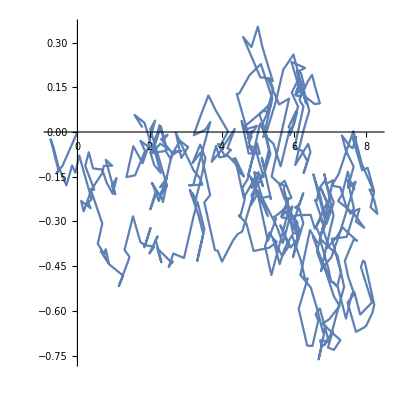

```mathematica
ListLinePlot[Trajs[[1]],AspectRatio->1,PlotRange->All]
```

```mathematica
sigma
```

0.154919

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\DA\\trajs.dat"];
```

```mathematica
Confined
```

```mathematica
NTrajs=10^4;
```

```mathematica
Trajs=Table[{0.0,0.0},{NTrajs},{len}];
```

```mathematica
For[i=1,i≤ NTrajs,i++,
B=RandomReal[{1,6}];
squaredrc=diffD*len*dt/B;
For[j=2,j≤ len,j++,
rr=RandomVariate[RayleighDistribution[sigma]];
theta=RandomReal[{0,2 Pi}];
rx=rr*Cos[theta];
ry=rr*Sin[theta];
tempx=Trajs[[i,j-1,1]]+rx;
tempy=Trajs[[i,j-1,2]]+ry;
If[(tempx^2+tempy^2)>squaredrc,
{a=Trajs[[i,j-1]];
t1=x/.Solve[(a[[1]]+x*Cos[theta])^2+(a[[2]]+x*Sin[theta])^2==squaredrc,x];
t2=Map[If[Abs[#]<10^-5,0,#]&,t1];
t=Sort[t2];
If[Length[t]==0,Print["no solution"];Print[rr];Print[t[[1]]];Print[theta,a];Print[squaredrc];];

tempx1=a[[1]]+t[[1]]*Cos[theta];
tempy1=a[[2]]+t[[1]]*Sin[theta];
tempx2=a[[1]]+t[[2]]*Cos[theta];
tempy2=a[[2]]+t[[2]]*Sin[theta];
dis=EuclideanDistance[{tempx1,tempy1},{tempx2,tempy2}];
ratio=(rr-t[[2]])/dis;

If[ratio>2,j=j-1;Continue[];];

ntempx=a[[1]]+(2*t[[2]]-rr)*Cos[theta];
ntempy=a[[2]]+(2*t[[2]]-rr)*Sin[theta];

If[(ntempx^2+ntempy^2)>squaredrc,
(*t1=x/.Solve[(ntempx+x*Cos[theta])^2+(ntempy+x*Sin[theta])^2==squaredrc,x];
t2=Map[If[Abs[#]<10^-5,0,#]&,t1];
t=Select[t2,1>#≥ 0&];
If[Length[t]==0,Print["no solution"]];*)
ntempx=tempx1+(rr-t[[2]]-dis)*Cos[theta];
ntempy=tempy1+(rr-t[[2]]-dis)*Sin[theta];

];
Trajs[[i,j,1]]=ntempx;
Trajs[[i,j,2]]=ntempy;
},
{Trajs[[i,j,1]]=tempx;
Trajs[[i,j,2]]=tempy;
}
]
]
]
```

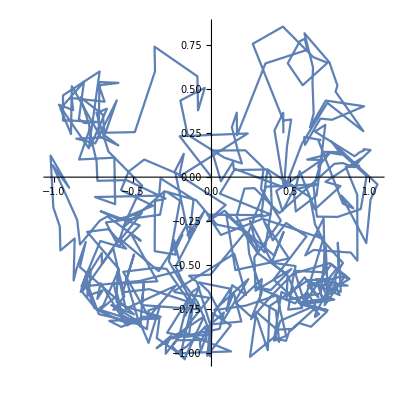

```mathematica
ListLinePlot[Trajs[[237]],AspectRatio->1,PlotRange->All]
```

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\Confined\\trajs.dat"];
```

```mathematica
ATTM
```

```mathematica
NTrajs=10^4;
Trajs=Table[{0.0,0.0},{NTrajs},{len}];
fixsigma=Sqrt[2*diffD*dt]
```

0.3

```mathematica
For[i=1,i≤ NTrajs,i++,
alpha=RandomReal[{0.3,1.0}];
dssig=RandomReal[{0.03,3.0}];
gamma=dssig/alpha;
While[(dssig>gamma)||(gamma>dssig+1),
{dssig=RandomReal[{0.03,3.0}];
gamma=dssig/alpha;}
];

step=1;
steps=1;
While[steps< len,
{ds=(1-RandomReal[{0.1,0.99}])^(1.0/dssig);
ts=ds^(-gamma);
While[(step== 1)&&(ts≥(len-1)),
{ds=(1-RandomReal[{0.1,0.99}])^(1.0/dssig);
ts=ds^(-gamma);}
];

If[ds<10^-3,ds=10^-3];
ts=ds^(-gamma);

tts=Floor[ts];

temp=steps;
steps=If[(temp+tts)>len,len,temp+tts];

sigma=Sqrt[2*ds*dt];

For[j=temp+1,j≤ steps,j++,
rr=RandomVariate[RayleighDistribution[sigma]];
If[rr<10^-6,Print[alpha,"/",dssig"/",i,"/""some diff",ds,"/",tts]];
theta=RandomReal[{0,2 Pi}];
rx=rr*Cos[theta];
ry=rr*Sin[theta];
Trajs[[i,j,1]]=Trajs[[i,j-1,1]]+rx;
Trajs[[i,j,2]]=Trajs[[i,j-1,2]]+ry;
];
step=step+1;}
];
randomx = RandomVariate[NormalDistribution[0,fixsigma/10],100];
randomy = RandomVariate[NormalDistribution[0,fixsigma/10],100];
Trajs[[i,All,1]]=MapThread[Plus, {Trajs[[i,All,1]], randomx}];
Trajs[[i,All,2]]=MapThread[Plus, {Trajs[[i,All,2]], randomy}];
]
```

```mathematica
Trajs[[1]]
```

{{0.016211,0.011711},{0.0103911,0.274323},{0.500969,-0.24669},{1.0892,-0.622789},{1.33317,-0.451586},{1.18952,-0.771025},{1.17964,-0.854152},{1.2478,-1.03967},{1.17683,-1.26453},{0.96967,-1.48037},{1.31073,-1.40797},{1.62479,-1.34661},{1.88805,-1.51563},{1.51493,-1.88869},{1.60822,-2.11565},{1.52641,-2.19842},{1.23712,-2.19847},{1.45848,-2.20473},{1.51829,-2.31591},{1.67641,-1.92657},{1.54018,-2.02387},{2.00221,-2.05842},{2.25068,-2.32925},{2.36537,-2.64433},{1.95263,-2.73551},{1.88242,-3.28913},{2.56595,-3.23077},{2.4452,-2.88258},{2.70377,-2.59195},{3.1105,-3.07566},{3.13357,-2.94213},{3.04021,-2.9869},{3.07481,-2.81922},{2.85333,-2.81896},{2.71972,-3.0504},{2.89156,-2.77308},{2.59092,-2.83331},{3.00035,-2.5028},{3.27596,-2.78706},{3.21193,-2.61518},{3.09311,-2.44484},{2.79945,-2.54544},{2.6794,-2.61722},{2.68846,-2.40428},{2.47895,-2.45862},{2.34609,-2.68012},{2.34337,-2.8655},{2.11414,-2.83542},{2.08187,-2.9113},{2.1324,-3.11979},{1.94927,-3.13572},{1.91778,-3.2206},{2.05242,-3.16938},{2.05346,-2.99185},{2.10382,-2.96337},{2.11041,-2.74909},{2.33119,-2.97741},{2.49494,-2.76504},{2.45896,-2.97229},{2.51065,-2.88916},{2.66961,-3.04701},{2.31169,-3.17204},{2.52125,-3.3676},{2.36097,-3.08059},{2.21746,-2.90865},{2.11891,-2.58642},{2.07797,-2.65315},{2.11537,-2.70485},{1.78156,-2.81544},{2.10779,-3.15538},{2.07868,-3.23778},{2.27145,-3.23252},{2.38551,-3.22433},{2.31086,-3.12256},{1.98214,-2.67939},{2.07354,-2.67736},{2.32412,-2.73141},{2.14416,-2.98765},{2.07356,-2.82806},{2.24226,-2.766},{2.29765,-2.49503},{2.64085,-2.55301},{3.13558,-2.29833},{3.30614,-2.03838},{3.33273,-1.92703},{3.05577,-2.05769},{3.08746,-1.77738},{2.75878,-1.67654},{2.16578,-1.24303},{2.05806,-1.19707},{1.82897,-1.56485},{1.86765,-1.44995},{2.52675,-1.57225},{2.68111,-1.68425},{2.35108,-1.16525},{2.73954,-1.33177},{2.95464,-1.16769},{2.94701,-0.83109},{2.15214,-1.00508},{1.98647,-0.771646}}

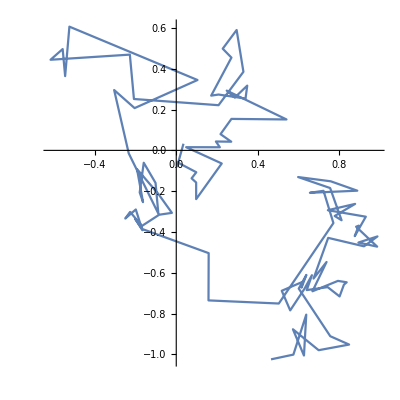

```mathematica
ListLinePlot[Trajs[[1000]],AspectRatio->1,PlotRange->All]
```

```mathematica
step
```

8

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\ATTM\\trajs_attm.dat"];
```

```mathematica
Export["E:\\KG\\Trajs\\ATTM\\ATTM.json",N[Trajs],"JSON"]
```

E:\KG\Trajs\ATTM\ATTM.json

```mathematica
SBM
```

```mathematica
NTrajs=1.5*10^4;
Trajs=Table[{0.0,0.0},{NTrajs},{len}];
sigma=Sqrt[2*diffD*dt]
fixsigma=Sqrt[2*diffD*dt]
```

0.3

0.3

```mathematica
For[i=1,i≤ NTrajs,i++,
alpha=RandomReal[{0.3,2.0}];
msd=Table[(sigma^2)*(j*dt)^alpha,{j,0,len}];
deltas=Sqrt[Differences[msd]];
randx=RandomReal[1,len];
dx=Sqrt[2]*deltas*InverseErfc[2-2*randx];
randy=RandomReal[1,len];
dy=Sqrt[2]*deltas*InverseErfc[2-2*randy];
Trajsx=Accumulate[dx];
Trajsy=Accumulate[dy];
traj=Transpose[{Trajsx,Trajsy}];
Trajs[[i]]=Map[#-traj[[1]]&,traj];

randomx = RandomVariate[NormalDistribution[0,fixsigma/10],100];
randomy = RandomVariate[NormalDistribution[0,fixsigma/10],100];
Trajs[[i,All,1]]=MapThread[Plus, {Trajs[[i,All,1]], randomx}];
Trajs[[i,All,2]]=MapThread[Plus, {Trajs[[i,All,2]], randomy}];
]
(*For[j=1,j≤ len,j++,
Trajs[[1,j,1]]=Trajsx[[j]]-Trajsx[[1]];
Trajs[[1,j,2]]=Trajsy[[j]]-Trajsy[[1]];
]*)
```

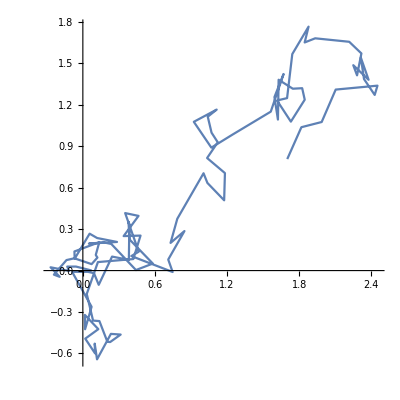

```mathematica
ListLinePlot[Trajs[[100]],AspectRatio->1,PlotRange->All]
```

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\SBM\\trajs.dat"];
```

```mathematica
Export["E:\\KG\\Trajs\\SBM\\SBM.json",N[Trajs],"JSON"]
```

E:\KG\Trajs\SBM\SBM.json

```mathematica
FBM
```

```mathematica
NTrajs=1.5*10^4;
Trajs=Table[{0.0,0.0},{NTrajs},{len}];
sigma=Sqrt[2*diffD*dt]
```

0.3

```mathematica
For[i=1,i≤ NTrajs,i++,
alpha=RandomReal[{0.2,1.99}];
While[alpha==1.0,alpha=RandomReal[{0.2,1.99}]];
Hurst=alpha/2.0;
data=RandomFunction[FractionalBrownianMotionProcess[0,sigma,Hurst],{0,99,1},2]["ValueList"];
Trajs[[i]]=Transpose[data];

randomx = RandomVariate[NormalDistribution[0,fixsigma/10],100];
randomy = RandomVariate[NormalDistribution[0,fixsigma/10],100];
Trajs[[i,All,1]]=MapThread[Plus, {Trajs[[i,All,1]], randomx}];
Trajs[[i,All,2]]=MapThread[Plus, {Trajs[[i,All,2]], randomy}];
]
```

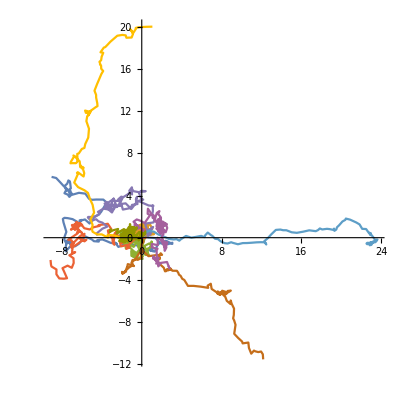

```mathematica
ListLinePlot[Trajs[[1;;10]],AspectRatio->1,PlotRange->All]
```

```mathematica
Export["E:\\KG\\Trajs\\FBM\\FBM.json",N[Trajs],"JSON"]
```

E:\KG\Trajs\FBM\FBM.json

```mathematica
sub_FBM
```

```mathematica
NTrajs=10^4;
Trajs=Table[{0.0,0.0},{NTrajs},{len}];
```

```mathematica
For[i=1,i≤ NTrajs,i++,
alpha=RandomReal[{0.2,0.99}];
Hurst=alpha/2.0;
data=RandomFunction[FractionalBrownianMotionProcess[0,sigma,Hurst],{0,499,1},2]["ValueList"];
Trajs[[i]]=Transpose[data];
]
```

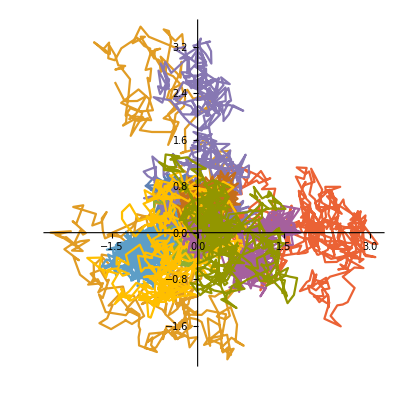

```mathematica
ListLinePlot[Trajs[[1;;10]],AspectRatio->1,PlotRange->All]
```

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\FBM\\trajs_sub.dat"];
```

```mathematica
super_FBM
```

```mathematica
NTrajs=10^4;
Trajs=Table[{0.0,0.0},{NTrajs},{len}];
```

```mathematica
For[i=1,i≤ NTrajs,i++,
alpha=RandomReal[{1.01,1.99}];
Hurst=alpha/2.0;
data=RandomFunction[FractionalBrownianMotionProcess[0,sigma,Hurst],{0,499,1},2]["ValueList"];
Trajs[[i]]=Transpose[data];
]
```

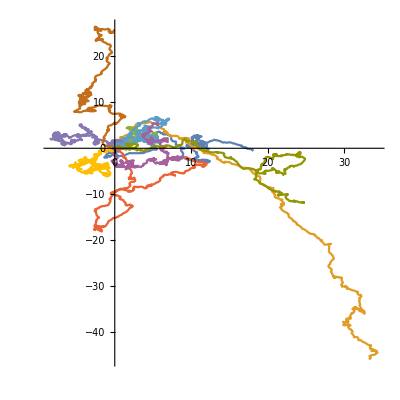

```mathematica
ListLinePlot[Trajs[[1;;10]],AspectRatio->1,PlotRange->All]
```

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\FBM\\trajs_sup.dat"];
```

```mathematica
Levy Walk
```

```mathematica
NTrajs=10000;
Trajs=Table[{0.0,0.0},{NTrajs},{len}];
```

```mathematica
For[i=1,i≤ NTrajs,i++,
alpha=RandomReal[{1.01,2}];
(*alpha=2;*)
If[alpha==2,timesig=RandomReal[{0.01,0.99}],timesig=3.0-alpha];
Twaiting=(1-RandomReal[])^(-1/timesig);
waitingsteps=Round[Twaiting];

While[waitingsteps≥ len,
Twaiting=(1-RandomReal[])^(-1/timesig);
waitingsteps=Floor[Twaiting];
];

t=1;

While[t≤ len,

R=RandomReal[{0.01,100}];
velo=If[RandomReal[]>0.5,Sqrt[R*diffD/dt],(-1)*Sqrt[R*diffD/dt]];
theta=RandomReal[{0,2*Pi}];

While[waitingsteps>0,
t=t+1;
If[t>len,Break[]];
Trajs[[i,t,1]]=Trajs[[i,t-1,1]]+velo*dt*Cos[theta];
Trajs[[i,t,2]]=Trajs[[i,t-1,2]]+velo*dt*Sin[theta];
waitingsteps--;
];
Twaiting=(1-RandomReal[])^(-1/timesig);
waitingsteps=Round[Twaiting];
];

randomx = RandomVariate[NormalDistribution[0,fixsigma/10],100];
randomy = RandomVariate[NormalDistribution[0,fixsigma/10],100];
Trajs[[i,All,1]]=MapThread[Plus, {Trajs[[i,All,1]], randomx}];
Trajs[[i,All,2]]=MapThread[Plus, {Trajs[[i,All,2]], randomy}];
]
```

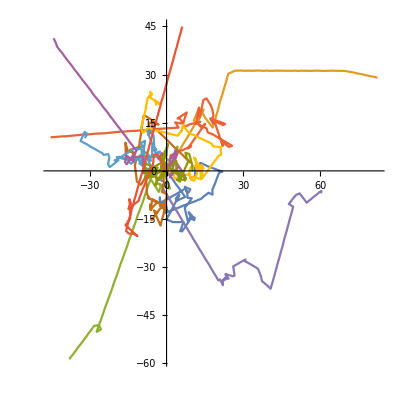

```mathematica
ListLinePlot[Trajs[[100;;110]],AspectRatio->1,PlotRange->All]
```

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\LW\\trajs_ball.dat"];
```

```mathematica
Export["E:\\KG\\Trajs\\LW\\LW.json",N[Trajs],"JSON"]
```

E:\KG\Trajs\LW\LW.json

```mathematica
Levy Flight
```

```mathematica
NTrajs=10^4;
Trajs=Table[{0.0,0.0},{NTrajs},{len}];
```

```mathematica
For[i=1,i≤ NTrajs,i++,
alpha=RandomReal[{0.9,2}];
For[j=2,j≤ len,j++,
rr=RandomVariate[StableDistribution[1,alpha,0,0,Sqrt[2*diffD*dt]]];
theta=RandomReal[{0,2 Pi}];
Trajs[[i,j,1]]=Trajs[[i,j-1,1]]+rr*Cos[theta];
Trajs[[i,j,2]]=Trajs[[i,j-1,2]]+rr*Sin[theta];
]
]
```

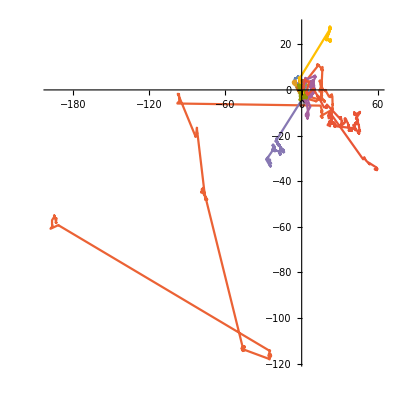

```mathematica
ListLinePlot[Trajs[[10;;20]],AspectRatio->1,PlotRange->All]
```

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\LF\\trajs.dat"];
```

```mathematica
data=Partition[Trajs[[10]],2,1];
deltax=Map[EuclideanDistance[#[[1]],#[[-1]]]&,data]
```

```mathematica
Length[Trajs[[10,501]]]
```

2

```mathematica
Position[deltax,Max[deltax]]
```

{{500}}

```mathematica
Trajs[[10,500;;501]]
```

{{6.07449,-0.681304},{0.,0.}}

```mathematica
diffD*Exp[2*0.01*0.681304]/2
```

0.202744

```mathematica
NTrajs=5000;
Trajs=Table[{0,0},{NTrajs},{len}];
```

```mathematica
trajs=Table[{0.0,0.0},{10*len}];
dt=0.003;
```

```mathematica
T1=AbsoluteTime[]
For[i=1,i≤ NTrajs,i++,
alpha=RandomReal[{0.2,2.0}];
trajs=Table[{0.0,0.0},{10*len}];
For[j=2,j≤ 10*len,j++,
tempx=trajs[[j-1,1]];
If[(-7≤ alpha*tempx≤ 7),difx=diffD*Exp[-2*alpha*(tempx/2)]/2,If[alpha*tempx>7,difx=diffD*Exp[-2*7]/2,difx=diffD*Exp[2*7]/2]];
trajs[[j,1]]=tempx+RandomVariate[NormalDistribution[0,Sqrt[2*difx*dt]]];
tempy=trajs[[j-1,2]];
If[(-7≤ alpha*tempy≤ 7),dify=diffD*Exp[-2*alpha*(tempy/2)]/2,If[alpha*tempy>7,dify=diffD*Exp[-2*7]/2,dify=diffD*Exp[2*7]/2]];
trajs[[j,2]]=tempy+RandomVariate[NormalDistribution[0,Sqrt[2*dify*dt]]]
];
For[k=2,k≤ len,k++,
Trajs[[i,k,1]]=trajs[[(k-1)*10,1]];
Trajs[[i,k,2]]=trajs[[(k-1)*10,2]];
]
]
T2=AbsoluteTime[]
```

3.918647715591×10^9

3.91864810096×10^9

```mathematica
T2-T1
```

391.067

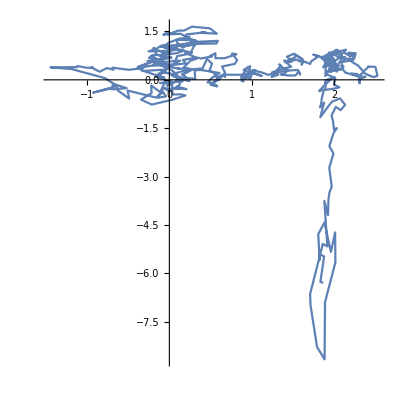

```mathematica
ListLinePlot[Trajs[[5000]],AspectRatio->1,PlotRange->All]
```

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\HDP\\trajs_exp_1.dat"];
```

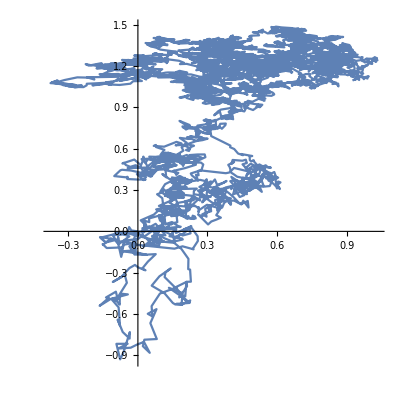

```mathematica
ListLinePlot[trajs,AspectRatio->1,PlotRange->All]
```

```mathematica
Clear[t]
```

```mathematica
alpha=1.0;
proc=StratonovichProcess[ⅆx[t]==√(diffD*Exp[-2*alpha*x[t]])ⅆw[t],x[t],{x,0},t,w\[Distributed]WienerProcess[]]
```

StratonovichProcess[{{0. √(ⅇ^(-2. x[t]))},{{0.632456 √(ⅇ^(-2. x[t]))}},x[t]},{{x},{0}},{t,0}]

```mathematica
data=Transpose[RandomFunction[proc,{0.,15,0.003},2]["ValueList"]];
```

```mathematica
Length[data]
```

5001

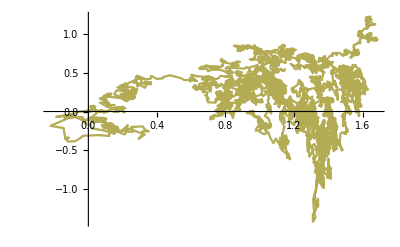

```mathematica
ListLinePlot[data,ColorFunction->"Rainbow",PlotRange->All]
```

```mathematica
data2=Partition[data,2,1];
```

```mathematica
deltax=Map[EuclideanDistance[#[[1]],#[[-1]]]&,data2];
```

```mathematica
RWFractal
```

```mathematica
p=0.6;
lx=500;
ly=500;
steps=5000;
Points=Table[0,{i,1,lx},{j,1,ly}];
pixel=Sqrt[2*diffD*dt/10]
```

0.0489898

```mathematica
NTrajs=10^4;
Trajs=Table[{0,0},{NTrajs},{len}];
```

```mathematica
T1=AbsoluteTime[]
For[i=1,i≤ NTrajs,i++,
percolationMatrix=RandomChoice[{1-p,p}->{0,1},{lx,ly}];
clusters=MorphologicalComponents[percolationMatrix,CornerNeighbors->False];
percolationClusters=ComponentMeasurements[clusters,{"Label","Count","BoundingBox"}];
maxCluster=MaximalBy[percolationClusters,#[[2,2]]&];
maxClusterLabel=maxCluster[[1,1]];
maxClusterPoints=Position[clusters,maxClusterLabel];
If[Length[maxClusterPoints]<10^4,Print["Something is wrong"];i=i-1;Continue[];];
Points=ReplacePart[ConstantArray[0,{lx,ly}],maxClusterPoints->1];

px=Nearest[maxClusterPoints[[All,1]],200][[1]];
py=Nearest[Select[maxClusterPoints,#[[1]]==px&][[All,2]],200][[1]];
If[Points[[px,py]]==0,Print["Something is wrong on initial point"];Break[]];
(*While[Points[[px,py]]==0,
px=RandomInteger[{100,150}];
py=RandomInteger[{100,150}];
];*)

steps=5000;
trajs=Table[{0,0},{steps}];

Trajs[[i,1,1]]=px*pixel;
Trajs[[i,1,2]]=py*pixel;
trajs[[1,1]]=px;
trajs[[1,2]]=py;
For[j=2,j≤ steps,j++,
tempx=trajs[[j-1,1]];
tempy=trajs[[j-1,2]];
If[(tempx==1||tempx== lx||tempy==1||tempy== ly),Print[i,"point boundary"];i=i-1;Break[]];
canpoint={{tempx-1,tempy,Points[[tempx-1,tempy]]},{tempx+1,tempy,Points[[tempx+1,tempy]]},{tempx,tempy-1,Points[[tempx,tempy-1]]},{tempx,tempy+1,Points[[tempx,tempy+1]]}};
If[MemberQ[canpoint[[All,3]],1],
{pos=Flatten[Position[canpoint[[All,3]],1]];
choice=RandomChoice[pos];
trajs[[j,1]]=canpoint[[choice,1]];
trajs[[j,2]]=canpoint[[choice,2]];},
Print[i,"not connection"];
i=i-1;
Break[]
]
];
For[k=2,k≤ len,k++,
Trajs[[i,k,1]]=trajs[[(k-1)*10,1]]*pixel;
Trajs[[i,k,2]]=trajs[[(k-1)*10,2]]*pixel;
];
If[Mod[i,100]==0,Print[i,"trajectory"]];
]
T2=AbsoluteTime[]
T2-T1
```

3.918550642135×10^9

100trajectory

200trajectory

300trajectory

400trajectory

500trajectory

600trajectory

700trajectory

800trajectory

900trajectory

1000trajectory

1100trajectory

1200trajectory

1300trajectory

1400trajectory

1500trajectory

1600trajectory

1700trajectory

1800trajectory

1900trajectory

2000trajectory

2100trajectory

2200trajectory

2300trajectory

2400trajectory

2500trajectory

2600trajectory

2700trajectory

2800trajectory

2900trajectory

3000trajectory

3100trajectory

3200trajectory

3300trajectory

3322point boundary

3400trajectory

3500trajectory

3600trajectory

3700trajectory

3800trajectory

3900trajectory

4000trajectory

4100trajectory

4200trajectory

4300trajectory

4400trajectory

4500trajectory

4600trajectory

4700trajectory

4800trajectory

4900trajectory

5000trajectory

5100trajectory

5123point boundary

5200trajectory

5300trajectory

5400trajectory

5500trajectory

5600trajectory

5700trajectory

5800trajectory

5900trajectory

6000trajectory

6100trajectory

6200trajectory

6300trajectory

6400trajectory

6500trajectory

6600trajectory

6700trajectory

6800trajectory

6900trajectory

7000trajectory

7100trajectory

7200trajectory

7300trajectory

7400trajectory

7500trajectory

7600trajectory

7700trajectory

7800trajectory

7900trajectory

8000trajectory

8100trajectory

8200trajectory

8300trajectory

8400trajectory

8500trajectory

8600trajectory

8700trajectory

8800trajectory

8900trajectory

9000trajectory

9100trajectory

9200trajectory

9300trajectory

9400trajectory

9500trajectory

9600trajectory

9700trajectory

9800trajectory

9900trajectory

10000trajectory

3.918555056673×10^9

4414.538

```mathematica
i=5122
```

5122

```mathematica
percolationMatrix=RandomChoice[{1-p,p}->{0,1},{lx,ly}];
clusters=MorphologicalComponents[percolationMatrix,CornerNeighbors->False];
percolationClusters=ComponentMeasurements[clusters,{"Label","Count","BoundingBox"}];
maxCluster=MaximalBy[percolationClusters,#[[2,2]]&];
maxClusterLabel=maxCluster[[1,1]];
maxClusterPoints=Position[clusters,maxClusterLabel];
If[Length[maxClusterPoints]<10^4,Print["Something is wrong"];i=i-1;Continue[];];
Points=ReplacePart[ConstantArray[0,{lx,ly}],maxClusterPoints->1];

px=Nearest[maxClusterPoints[[All,1]],200][[1]];
py=Nearest[Select[maxClusterPoints,#[[1]]==px&][[All,2]],200][[1]];
If[Points[[px,py]]==0,Print["Something is wrong on initial point"];Break[]];
(*While[Points[[px,py]]==0,
px=RandomInteger[{100,150}];
py=RandomInteger[{100,150}];
];*)

steps=5000;
trajs=Table[{0,0},{steps}];

Trajs[[i,1,1]]=px*pixel;
Trajs[[i,1,2]]=py*pixel;
trajs[[1,1]]=px;
trajs[[1,2]]=py;
For[j=2,j≤ steps,j++,
tempx=trajs[[j-1,1]];
tempy=trajs[[j-1,2]];
If[(tempx==1||tempx== lx||tempy==1||tempy== ly),Print[i,"point boundary"];i=i-1;Break[]];
canpoint={{tempx-1,tempy,Points[[tempx-1,tempy]]},{tempx+1,tempy,Points[[tempx+1,tempy]]},{tempx,tempy-1,Points[[tempx,tempy-1]]},{tempx,tempy+1,Points[[tempx,tempy+1]]}};
If[MemberQ[canpoint[[All,3]],1],
{pos=Flatten[Position[canpoint[[All,3]],1]];
choice=RandomChoice[pos];
trajs[[j,1]]=canpoint[[choice,1]];
trajs[[j,2]]=canpoint[[choice,2]];},
Print[i,"not connection"];
i=i-1;
Break[]
]
];
For[k=2,k≤ len,k++,
Trajs[[i,k,1]]=trajs[[(k-1)*10,1]]*pixel;
Trajs[[i,k,2]]=trajs[[(k-1)*10,2]]*pixel;
];
```

```mathematica
Trajs[[5122]]
```

{{9.79796,9.89594},{9.69998,10.0429},{9.69998,10.0429},{9.79796,9.94493},{9.79796,9.94493},{9.79796,9.94493},{9.84695,9.89594},{9.79796,9.94493},{9.79796,9.94493},{9.74897,9.99392},{9.79796,9.94493},{9.79796,9.94493},{9.79796,9.94493},{9.69998,10.0429},{9.79796,10.1409},{9.74897,10.0919},{9.74897,10.1899},{9.74897,10.0919},{9.74897,10.1899},{9.79796,10.0429},{9.79796,10.0429},{9.79796,10.0429},{9.602,10.1409},{9.602,10.0429},{9.55301,10.0919},{9.35705,10.1899},{9.25907,10.1899},{9.25907,9.99392},{9.30806,9.94493},{9.30806,9.94493},{9.25907,9.99392},{9.35705,9.99392},{9.21008,9.94493},{9.16109,9.89594},{9.16109,9.89594},{9.25907,9.99392},{9.25907,10.0919},{9.1121,9.94493},{9.1121,9.84695},{9.16109,9.89594},{9.21008,9.94493},{9.16109,9.89594},{9.16109,9.89594},{9.06311,9.79796},{9.16109,9.89594},{9.06311,9.79796},{9.16109,9.89594},{9.25907,9.99392},{9.25907,10.0919},{9.25907,9.99392},{9.1121,9.84695},{9.06311,9.79796},{9.1121,9.94493},{9.1121,9.84695},{9.1121,9.84695},{9.06311,9.79796},{9.16109,9.89594},{9.30806,9.94493},{9.21008,9.94493},{9.1121,9.84695},{9.1121,9.94493},{9.1121,9.94493},{9.06311,9.79796},{9.1121,9.84695},{9.16109,9.89594},{9.1121,9.84695},{9.21008,9.94493},{9.30806,9.94493},{9.25907,9.99392},{9.21008,9.94493},{9.25907,9.99392},{9.25907,9.99392},{9.25907,9.99392},{9.30806,9.94493},{9.16109,9.89594},{9.06311,9.79796},{9.06311,9.79796},{9.1121,9.94493},{9.16109,9.89594},{9.06311,9.79796},{9.30806,9.94493},{9.30806,9.94493},{9.30806,9.94493},{9.35705,9.99392},{9.35705,9.99392},{9.35705,9.99392},{9.35705,9.99392},{9.35705,9.99392},{9.35705,9.99392},{9.30806,9.94493},{9.35705,9.99392},{9.1121,9.94493},{9.1121,9.84695},{9.16109,9.89594},{9.16109,9.99392},{9.1121,9.84695},{9.1121,9.84695},{9.1121,9.84695},{9.35705,9.99392},{9.30806,9.84695},{9.30806,9.84695},{9.30806,9.84695},{9.30806,9.84695},{9.30806,9.84695},{9.25907,9.99392},{9.30806,9.94493},{9.30806,9.84695},{9.30806,9.84695},{9.30806,9.94493},{9.21008,9.94493},{9.16109,9.99392},{9.16109,9.89594},{9.16109,9.99392},{9.16109,9.99392},{9.1121,9.94493},{9.30806,9.94493},{9.30806,9.94493},{9.16109,9.89594},{9.1121,9.94493},{9.16109,9.89594},{9.35705,9.99392},{9.35705,9.99392},{9.30806,9.84695},{9.30806,9.84695},{9.30806,9.94493},{9.21008,9.94493},{9.16109,10.0919},{9.06311,10.0919},{9.1121,10.1409},{9.06311,10.0919},{8.96513,9.99392},{9.06311,10.0919},{8.91614,10.0429},{8.86715,10.0919},{8.96513,10.0919},{8.86715,10.0919},{8.81816,10.0429},{8.86715,10.0919},{8.76917,10.0919},{8.76917,10.0919},{8.81816,10.0429},{8.81816,10.0429},{8.81816,10.0429},{8.86715,10.0919},{8.81816,10.0429},{8.91614,10.1409},{8.86715,10.1899},{9.01412,10.0429},{9.01412,10.0429},{9.01412,10.0429},{8.86715,9.89594},{8.96513,9.99392},{8.96513,9.99392},{8.86715,9.79796},{8.86715,9.79796},{8.91614,9.94493},{8.96513,9.99392},{8.86715,9.89594},{8.96513,9.99392},{9.06311,9.99392},{8.96513,9.99392},{8.91614,9.94493},{9.01412,10.0429},{9.16109,10.0919},{9.1121,10.1409},{9.1121,10.1409},{9.16109,10.0919},{9.16109,10.0919},{9.21008,9.94493},{9.16109,9.99392},{9.35705,9.99392},{9.21008,9.94493},{9.06311,9.79796},{9.1121,9.94493},{9.06311,9.79796},{9.1121,9.84695},{9.16109,9.89594},{9.16109,9.89594},{9.1121,9.94493},{9.1121,9.94493},{9.35705,9.99392},{9.35705,9.99392},{9.30806,9.94493},{9.25907,9.99392},{9.35705,9.99392},{9.30806,9.94493},{9.30806,10.1409},{9.30806,10.1409},{9.25907,10.1899},{9.35705,10.1899},{9.45503,10.0919},{9.55301,10.0919},{9.45503,10.0919},{9.55301,10.1899},{9.55301,10.3858},{9.50402,10.3368},{9.50402,10.2389},{9.55301,10.3858},{9.602,10.3368},{9.602,10.5328},{9.65099,10.4838},{9.65099,10.4838},{9.602,10.5328},{9.65099,10.5818},{9.65099,10.6798},{9.602,10.5328},{9.50402,10.5328},{9.45503,10.5818},{9.50402,10.5328},{9.45503,10.4838},{9.40604,10.4348},{9.35705,10.3858},{9.602,10.5328},{9.35705,10.5818},{9.35705,10.6798},{9.35705,10.5818},{9.35705,10.6798},{9.45503,10.5818},{9.35705,10.5818},{9.35705,10.5818},{9.40604,10.6308},{9.35705,10.5818},{9.45503,10.5818},{9.45503,10.5818},{9.50402,10.4348},{9.55301,10.4838},{9.65099,10.4838},{9.65099,10.4838},{9.65099,10.5818},{9.79796,10.5328},{9.79796,10.5328},{9.79796,10.8267},{9.79796,10.7288},{9.69998,10.5328},{9.65099,10.3858},{9.74897,10.3858},{9.65099,10.3858},{9.69998,10.4348},{9.65099,10.3858},{9.69998,10.3368},{9.65099,10.1899},{9.69998,10.1409},{9.74897,10.2879},{9.65099,10.2879},{9.74897,10.2879},{9.84695,10.2879},{9.84695,10.2879},{9.84695,10.2879},{9.84695,10.2879},{9.84695,10.3858},{9.84695,10.3858},{9.84695,10.3858},{9.84695,10.2879},{9.65099,10.3858},{9.602,10.3368},{9.50402,10.2389},{9.74897,10.0919},{9.65099,10.0919},{9.65099,10.1899},{9.69998,10.2389},{9.74897,10.1899},{9.79796,10.0429},{9.69998,10.0429},{9.74897,10.1899},{9.65099,10.1899},{9.74897,10.2879},{9.84695,10.2879},{9.84695,10.2879},{9.69998,10.2389},{9.74897,10.2879},{9.55301,10.3858},{9.65099,10.2879},{9.65099,10.2879},{9.74897,10.0919},{9.65099,10.1899},{9.69998,10.1409},{9.79796,10.1409},{9.69998,10.1409},{9.69998,10.2389},{9.74897,10.1899},{9.74897,10.1899},{9.55301,10.1899},{9.602,10.1409},{9.65099,10.0919},{9.69998,10.3368},{9.79796,10.5328},{9.79796,10.6308},{9.79796,10.6308},{9.69998,10.5328},{9.69998,10.5328},{9.65099,10.4838},{9.50402,10.4348},{9.50402,10.3368},{9.40604,10.4348},{9.45503,10.4838},{9.45503,10.4838},{9.45503,10.4838},{9.50402,10.4348},{9.50402,10.4348},{9.602,10.3368},{9.50402,10.4348},{9.50402,10.4348},{9.55301,10.1899},{9.74897,10.1899},{9.79796,10.1409},{9.69998,10.2389},{9.602,10.3368},{9.65099,10.3858},{9.74897,10.2879},{9.84695,10.3858},{9.84695,10.2879},{9.69998,10.3368},{9.65099,10.2879},{9.65099,10.0919},{9.84695,10.2879},{9.69998,10.4348},{9.69998,10.4348},{9.65099,10.5818},{9.69998,10.5328},{9.65099,10.2879},{9.74897,10.3858},{9.65099,10.3858},{9.74897,10.3858},{9.74897,10.2879},{9.74897,10.2879},{9.84695,10.2879},{9.74897,10.1899},{9.69998,10.2389},{9.74897,10.2879},{9.65099,10.3858},{9.69998,10.4348},{9.65099,10.4838},{9.69998,10.5328},{9.65099,10.6798},{9.69998,10.7288},{9.65099,10.6798},{9.602,10.9247},{9.45503,10.9737},{9.40604,10.9247},{9.30806,11.0227},{9.45503,10.9737},{9.45503,10.9737},{9.45503,11.0717},{9.30806,11.0227},{9.30806,10.9247},{9.40604,10.9247},{9.30806,10.9247},{9.45503,11.0717},{9.55301,11.0717},{9.55301,11.0717},{9.55301,11.0717},{9.50402,11.1207},{9.65099,11.1697},{9.50402,11.1207},{9.55301,11.0717},{9.40604,11.0227},{9.40604,11.0227},{9.40604,11.0227},{9.50402,10.9247},{9.50402,10.9247},{9.40604,11.0227},{9.45503,11.0717},{9.30806,11.0227},{9.40604,11.1207},{9.40604,11.1207},{9.30806,11.0227},{9.45503,11.0717},{9.45503,10.9737},{9.65099,10.9737},{9.602,10.9247},{9.69998,10.7288},{9.65099,10.6798},{9.65099,10.5818},{9.79796,10.6308},{9.74897,10.3858},{9.84695,10.2879},{9.69998,10.1409},{9.74897,10.2879},{9.65099,10.3858},{9.602,10.1409},{9.55301,10.0919},{9.602,10.1409},{9.74897,10.2879},{9.74897,10.0919},{9.74897,10.0919},{9.602,10.1409},{9.602,10.0429},{9.45503,10.0919},{9.35705,10.1899},{9.25907,10.1899},{9.25907,10.1899},{9.1121,10.2389},{9.1121,10.2389},{9.06311,10.2879},{9.06311,10.4838},{8.96513,10.4838},{8.96513,10.4838},{9.06311,10.3858},{9.30806,10.4348},{9.21008,10.4348},{9.21008,10.5328},{9.30806,10.4348},{9.21008,10.3368},{9.25907,10.2879},{9.01412,10.2389},{9.06311,10.2879},{9.06311,10.2879},{8.96513,10.5818},{8.96513,10.5818},{8.91614,10.5328},{9.06311,10.3858},{9.01412,10.4348},{9.06311,10.3858},{9.21008,10.5328},{9.1121,10.6308},{9.16109,10.5818},{9.25907,10.6798},{9.16109,10.6798},{9.21008,10.7288},{9.1121,10.6308},{9.1121,10.6308},{9.21008,10.5328},{9.1121,10.4348},{9.1121,10.3368},{9.06311,10.2879},{8.96513,10.2879},{8.91614,10.1409},{8.96513,10.1899},{8.86715,10.1899},{8.91614,10.1409},{8.96513,10.1899},{8.91614,10.2389},{8.96513,10.1899},{8.91614,10.1409},{8.86715,10.1899},{8.86715,10.1899},{8.91614,10.2389},{8.86715,10.1899},{8.91614,10.0429},{8.76917,10.0919},{8.76917,10.0919},{8.91614,10.0429},{8.96513,9.99392},{8.96513,9.99392},{8.91614,9.94493},{8.96513,9.89594},{8.81816,10.0429},{8.91614,9.94493},{8.96513,9.89594},{8.86715,9.89594},{8.91614,9.94493},{8.96513,9.99392},{8.91614,10.0429},{8.86715,10.0919},{8.91614,10.1409},{8.96513,10.2879},{8.96513,10.2879},{9.06311,10.2879},{9.06311,10.2879},{8.96513,10.1899},{8.91614,10.1409},{8.91614,10.1409},{8.91614,10.1409},{8.96513,10.1899},{8.96513,10.0919},{8.96513,10.2879},{9.06311,10.3858},{9.21008,10.3368},{9.30806,10.4348},{9.30806,10.5328},{9.21008,10.5328},{9.25907,10.3858},{9.21008,10.2389},{9.21008,10.2389},{9.21008,10.3368},{9.30806,10.1409},{9.40604,10.2389},{9.35705,10.1899},{9.35705,10.1899},{9.55301,10.1899},{9.65099,10.0919},{9.65099,10.1899},{9.69998,10.1409},{9.45503,10.0919},{9.65099,10.0919},{9.55301,10.1899},{9.69998,10.1409},{9.65099,10.0919},{9.79796,10.1409},{9.79796,10.0429},{9.69998,10.0429},{9.79796,10.1409},{9.69998,10.0429},{9.69998,10.0429},{9.69998,10.2389},{9.602,10.1409},{9.602,10.0429},{9.55301,10.0919},{9.602,10.0429},{9.65099,10.1899}}

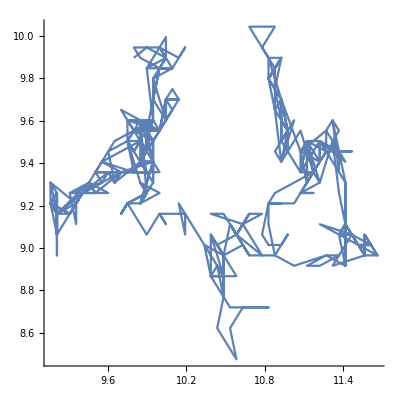

```mathematica
ListLinePlot[Trajs[[5123]],AspectRatio->1,PlotRange->All]
```

```mathematica
Count[Points,1,2]
```

16922

```mathematica
ArrayPlot[Points,ColorFunction->"Rainbow"]
```

-Graphics-

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\RWF\\trajs.dat"];
```

```mathematica
CTRW
```

```mathematica
NTrajs=10^4;
Trajs=Table[{0,0},{NTrajs},{len+1}];
fixsigma
sigma
```

0.3

0.3

```mathematica
T1=AbsoluteTime[]
For[i=1,i≤ NTrajs,i++,
alpha=RandomReal[{0.3,0.99}];
(*alpha=RandomReal[{1.0,2.0}];*)
times=(1-RandomReal[{0,1},len])^(-1/alpha);

Time=Accumulate[times];
step=Select[Time,#≤ len&];
If[Length[step]==0,
Print[i,"No jump"];i=i-1;Continue[];
];

steplength=RandomVariate[NormalDistribution[0,sigma],{Length[step],2}];
trajs=Accumulate[steplength];

PrependTo[step,0];
AppendTo[step,len];
step=step+1;

trajs=Prepend[trajs,{0,0}];

For[j=1,j≤ Length[step]-1,j++,
waiting=Ceiling[step[[j]]];
jump=Floor[step[[j+1]]];
For[k=waiting,k≤ jump,k++,
Trajs[[i,k,1]]=trajs[[j,1]];
Trajs[[i,k,2]]=trajs[[j,2]];
]
];
randomx = RandomVariate[NormalDistribution[0,fixsigma/10],101];
randomy = RandomVariate[NormalDistribution[0,fixsigma/10],101];
Trajs[[i,All,1]]=MapThread[Plus, {Trajs[[i,All,1]], randomx}];
Trajs[[i,All,2]]=MapThread[Plus, {Trajs[[i,All,2]], randomy}];
]
T2=AbsoluteTime[]
T2-T1
```

3.951800244557×10^9

7No jump

11No jump

38No jump

39No jump

46No jump

53No jump

56No jump

95No jump

101No jump

110No jump

162No jump

228No jump

230No jump

274No jump

275No jump

308No jump

320No jump

330No jump

339No jump

391No jump

401No jump

405No jump

412No jump

416No jump

416No jump

422No jump

500No jump

532No jump

532No jump

532No jump

552No jump

552No jump

555No jump

555No jump

564No jump

577No jump

579No jump

579No jump

602No jump

602No jump

606No jump

607No jump

617No jump

646No jump

650No jump

650No jump

656No jump

665No jump

672No jump

681No jump

705No jump

709No jump

721No jump

749No jump

755No jump

761No jump

791No jump

800No jump

803No jump

827No jump

841No jump

855No jump

867No jump

873No jump

873No jump

893No jump

898No jump

933No jump

978No jump

996No jump

1006No jump

1029No jump

1048No jump

1076No jump

1092No jump

1098No jump

1126No jump

1145No jump

1149No jump

1154No jump

1172No jump

1187No jump

1190No jump

1195No jump

1205No jump

1215No jump

1255No jump

1269No jump

1279No jump

1279No jump

1292No jump

1309No jump

1337No jump

1350No jump

1350No jump

1364No jump

1376No jump

1376No jump

1376No jump

1387No jump

1390No jump

1397No jump

1397No jump

1401No jump

1407No jump

1493No jump

1495No jump

1495No jump

1499No jump

1513No jump

1514No jump

1537No jump

1558No jump

1565No jump

1566No jump

1606No jump

1606No jump

1608No jump

1611No jump

1613No jump

1623No jump

1675No jump

1724No jump

1732No jump

1739No jump

1767No jump

1787No jump

1800No jump

1819No jump

1824No jump

1834No jump

1834No jump

1845No jump

1847No jump

1873No jump

1879No jump

1880No jump

1908No jump

1908No jump

1946No jump

1975No jump

1979No jump

1983No jump

1991No jump

2004No jump

2010No jump

2014No jump

2017No jump

2019No jump

2039No jump

2079No jump

2094No jump

2102No jump

2103No jump

2140No jump

2150No jump

2170No jump

2192No jump

2196No jump

2265No jump

2296No jump

2303No jump

2348No jump

2380No jump

2391No jump

2396No jump

2412No jump

2422No jump

2466No jump

2489No jump

2489No jump

2491No jump

2503No jump

2524No jump

2524No jump

2532No jump

2567No jump

2609No jump

2610No jump

2610No jump

2629No jump

2637No jump

2637No jump

2660No jump

2675No jump

2676No jump

2685No jump

2715No jump

2721No jump

2744No jump

2764No jump

2827No jump

2830No jump

2839No jump

2848No jump

2852No jump

2854No jump

2863No jump

2875No jump

2903No jump

2930No jump

2930No jump

2963No jump

2967No jump

2972No jump

2984No jump

2992No jump

2993No jump

3001No jump

3007No jump

3019No jump

3062No jump

3064No jump

3076No jump

3079No jump

3095No jump

3098No jump

3103No jump

3103No jump

3111No jump

3122No jump

3133No jump

3149No jump

3187No jump

3193No jump

3196No jump

3201No jump

3205No jump

3214No jump

3230No jump

3232No jump

3245No jump

3280No jump

3287No jump

3296No jump

3303No jump

3304No jump

3320No jump

3323No jump

3330No jump

3345No jump

3351No jump

3359No jump

3363No jump

3365No jump

3374No jump

3390No jump

3401No jump

3408No jump

3487No jump

3514No jump

3543No jump

3566No jump

3568No jump

3615No jump

3666No jump

3668No jump

3670No jump

3677No jump

3685No jump

3706No jump

3718No jump

3719No jump

3732No jump

3744No jump

3748No jump

3755No jump

3768No jump

3791No jump

3842No jump

3849No jump

3856No jump

3856No jump

3859No jump

3861No jump

3871No jump

3873No jump

3883No jump

3927No jump

3929No jump

3933No jump

3936No jump

3937No jump

3971No jump

4000No jump

4003No jump

4010No jump

4032No jump

4032No jump

4056No jump

4095No jump

4102No jump

4111No jump

4111No jump

4114No jump

4122No jump

4139No jump

4153No jump

4173No jump

4199No jump

4227No jump

4246No jump

4253No jump

4276No jump

4280No jump

4291No jump

4328No jump

4348No jump

4355No jump

4363No jump

4377No jump

4404No jump

4404No jump

4406No jump

4412No jump

4413No jump

4415No jump

4415No jump

4460No jump

4461No jump

4468No jump

4468No jump

4473No jump

4488No jump

4495No jump

4567No jump

4580No jump

4615No jump

4621No jump

4625No jump

4651No jump

4651No jump

4651No jump

4692No jump

4715No jump

4717No jump

4722No jump

4724No jump

4754No jump

4761No jump

4765No jump

4780No jump

4799No jump

4814No jump

4829No jump

4829No jump

4833No jump

4855No jump

4882No jump

4889No jump

4890No jump

4896No jump

4910No jump

4911No jump

4935No jump

4942No jump

4950No jump

4956No jump

4974No jump

4981No jump

4987No jump

4991No jump

4993No jump

4993No jump

5018No jump

5021No jump

5024No jump

5040No jump

5056No jump

5067No jump

5074No jump

5077No jump

5077No jump

5096No jump

5119No jump

5121No jump

5122No jump

5143No jump

5147No jump

5148No jump

5170No jump

5175No jump

5182No jump

5197No jump

5206No jump

5240No jump

5245No jump

5257No jump

5273No jump

5281No jump

5293No jump

5295No jump

5299No jump

5305No jump

5334No jump

5335No jump

5339No jump

5342No jump

5364No jump

5371No jump

5395No jump

5397No jump

5402No jump

5407No jump

5433No jump

5466No jump

5474No jump

5492No jump

5508No jump

5508No jump

5508No jump

5513No jump

5525No jump

5539No jump

5547No jump

5552No jump

5581No jump

5595No jump

5604No jump

5604No jump

5618No jump

5640No jump

5642No jump

5664No jump

5674No jump

5677No jump

5694No jump

5700No jump

5708No jump

5723No jump

5728No jump

5734No jump

5765No jump

5767No jump

5774No jump

5782No jump

5794No jump

5796No jump

5820No jump

5863No jump

5867No jump

5889No jump

5898No jump

5898No jump

5913No jump

5920No jump

5924No jump

5932No jump

5935No jump

5944No jump

5963No jump

5965No jump

5970No jump

5979No jump

6003No jump

6008No jump

6018No jump

6067No jump

6068No jump

6095No jump

6101No jump

6121No jump

6121No jump

6123No jump

6123No jump

6125No jump

6146No jump

6165No jump

6189No jump

6213No jump

6216No jump

6221No jump

6234No jump

6250No jump

6263No jump

6267No jump

6280No jump

6289No jump

6319No jump

6322No jump

6322No jump

6330No jump

6434No jump

6436No jump

6441No jump

6442No jump

6458No jump

6487No jump

6498No jump

6510No jump

6523No jump

6523No jump

6534No jump

6567No jump

6587No jump

6594No jump

6617No jump

6621No jump

6678No jump

6679No jump

6691No jump

6708No jump

6727No jump

6734No jump

6763No jump

6782No jump

6793No jump

6796No jump

6815No jump

6819No jump

6851No jump

6860No jump

6884No jump

6890No jump

6920No jump

6942No jump

6961No jump

6971No jump

6971No jump

6985No jump

6989No jump

6990No jump

7000No jump

7016No jump

7022No jump

7030No jump

7032No jump

7033No jump

7051No jump

7069No jump

7072No jump

7079No jump

7082No jump

7088No jump

7091No jump

7098No jump

7128No jump

7179No jump

7202No jump

7218No jump

7228No jump

7238No jump

7238No jump

7249No jump

7268No jump

7272No jump

7279No jump

7283No jump

7290No jump

7305No jump

7306No jump

7321No jump

7343No jump

7354No jump

7355No jump

7367No jump

7368No jump

7382No jump

7382No jump

7382No jump

7395No jump

7398No jump

7406No jump

7409No jump

7409No jump

7413No jump

7416No jump

7439No jump

7447No jump

7487No jump

7501No jump

7524No jump

7527No jump

7543No jump

7546No jump

7565No jump

7572No jump

7582No jump

7596No jump

7602No jump

7608No jump

7622No jump

7633No jump

7655No jump

7678No jump

7687No jump

7699No jump

7699No jump

7713No jump

7745No jump

7746No jump

7802No jump

7842No jump

7847No jump

7852No jump

7872No jump

7884No jump

7891No jump

7899No jump

7901No jump

7911No jump

7915No jump

7932No jump

7938No jump

7939No jump

7952No jump

7972No jump

8012No jump

8024No jump

8024No jump

8037No jump

8041No jump

8047No jump

8058No jump

8088No jump

8106No jump

8112No jump

8133No jump

8137No jump

8148No jump

8162No jump

8182No jump

8183No jump

8191No jump

8200No jump

8201No jump

8212No jump

8227No jump

8237No jump

8265No jump

8276No jump

8279No jump

8304No jump

8307No jump

8308No jump

8309No jump

8309No jump

8312No jump

8317No jump

8346No jump

8348No jump

8359No jump

8361No jump

8370No jump

8372No jump

8377No jump

8391No jump

8406No jump

8413No jump

8442No jump

8455No jump

8466No jump

8466No jump

8471No jump

8484No jump

8489No jump

8496No jump

8510No jump

8516No jump

8524No jump

8540No jump

8543No jump

8549No jump

8563No jump

8570No jump

8571No jump

8574No jump

8577No jump

8584No jump

8598No jump

8602No jump

8620No jump

8622No jump

8624No jump

8634No jump

8649No jump

8663No jump

8669No jump

8675No jump

8722No jump

8727No jump

8728No jump

8760No jump

8763No jump

8771No jump

8781No jump

8801No jump

8802No jump

8813No jump

8814No jump

8827No jump

8853No jump

8887No jump

8902No jump

8918No jump

8923No jump

8925No jump

8926No jump

8939No jump

8954No jump

8954No jump

8955No jump

8977No jump

9020No jump

9058No jump

9061No jump

9069No jump

9118No jump

9122No jump

9130No jump

9147No jump

9154No jump

9162No jump

9162No jump

9165No jump

9170No jump

9193No jump

9218No jump

9227No jump

9233No jump

9235No jump

9236No jump

9296No jump

9309No jump

9317No jump

9350No jump

9368No jump

9380No jump

9381No jump

9384No jump

9396No jump

9413No jump

9428No jump

9434No jump

9446No jump

9447No jump

9447No jump

9448No jump

9486No jump

9488No jump

9506No jump

9511No jump

9581No jump

9600No jump

9611No jump

9631No jump

9632No jump

9632No jump

9632No jump

9651No jump

9676No jump

9710No jump

9712No jump

9717No jump

9723No jump

9726No jump

9730No jump

9736No jump

9750No jump

9764No jump

9768No jump

9806No jump

9846No jump

9873No jump

9879No jump

9890No jump

9903No jump

9909No jump

9927No jump

9939No jump

9946No jump

9953No jump

9953No jump

9966No jump

9966No jump

9988No jump

9989No jump

3.951800255156×10^9

10.599

```mathematica
MemberQ[Trajs[[9860,All,1]],Except[0]]
```

True

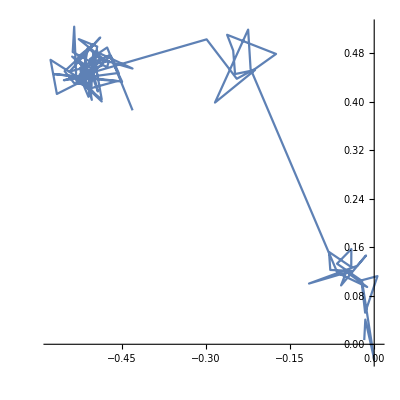

```mathematica
ListLinePlot[Trajs[[4185]],AspectRatio->1,PlotRange->All]
```

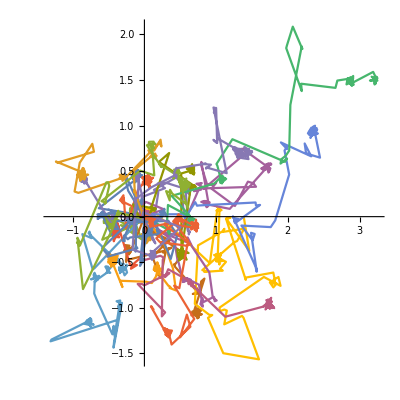

```mathematica
ListLinePlot[Trajs[[1;;20]],AspectRatio->1,PlotRange->All]
```

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\CTRW\\trajs_sub.dat"];
```

```mathematica
Export["E:\\KG\\Trajs\\CTRW\\CTRW.json",N[Trajs],"JSON"]
```

E:\KG\Trajs\CTRW\CTRW.json

```mathematica
T1=AbsoluteTime[]
For[i=1,i≤ NTrajs,i++,
waittimesig=5;
times={0};
t=0;
temptime=0;
While[t≤len,
waitting=RandomVariate[NormalDistribution[0.001,waittimesig]];
temptime=Abs[temptime+waitting];
t=t+temptime;
AppendTo[times,temptime];
];

Time=Accumulate[times];
Time[[-1]]=len;
step=Time+1;
If[Length[step]≤ 2,Print[i,"No jump"];i=i-1;Continue[];];

(*steplength=RandomReal[NormalDistribution[0,sigma],{Length[step-2],2}];*)
steplength=RandomVariate[RayleighDistribution[2*sigma],Length[step-2]];
stepjump=Table[{0,0},{Length[steplength]}];
For[k=1,k≤ Length[steplength],k++,
theta=RandomReal[{0,2*Pi}];
stepjump[[k,1]]=steplength[[k]]*Cos[theta];
stepjump[[k,2]]=steplength[[k]]*Sin[theta];
];

(*trajs=Accumulate[steplength];*)
trajs=Accumulate[stepjump];

trajs=Prepend[trajs,{0,0}];

For[j=1,j≤ Length[step]-1,j++,
waiting=Ceiling[step[[j]]];
jump=Floor[step[[j+1]]];
For[k=waiting,k≤ jump,k++,
Trajs[[i,k,1]]=trajs[[j,1]];
Trajs[[i,k,2]]=trajs[[j,2]];
]
]
]
T2=AbsoluteTime[]
T2-T1
```

3.918646020238×10^9

3.918646037975×10^9

17.737

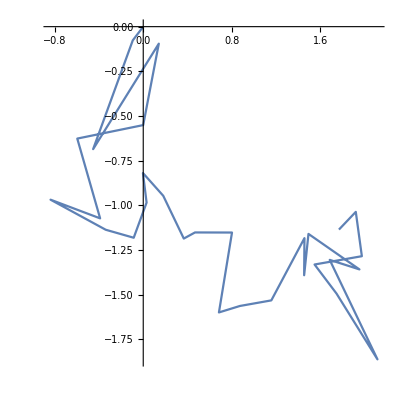

```mathematica
ListLinePlot[Trajs[[1000]],AspectRatio->1,PlotRange->All]
```

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\CTRW\\trajs_cor_Gau.dat"];
```

```mathematica
Correlated CTRW Levy
```

```mathematica
NTrajs=10^4;
Trajs=Table[{0,0},{NTrajs},{len+1}];
```

```mathematica
T1=AbsoluteTime[]
For[i=1,i≤ NTrajs,i++,
waittimesig=2;
gamma=RandomReal[{0.3,2.0}];
times={0};
t=0;
temptime=0;
While[t≤len,
waitting=RandomVariate[StableDistribution[1,gamma,0,0,waittimesig]];
temptime=Abs[temptime+waitting];
t=t+temptime;
AppendTo[times,temptime];
];

Time=Accumulate[times];
Time[[-1]]=len;
step=Time+1;
If[Length[step]≤ 2,Print[i,"No jump"];i=i-1;Continue[];];

(*steplength=RandomReal[NormalDistribution[0,sigma],{Length[step-2],2}];*)
steplength=RandomVariate[RayleighDistribution[2*sigma],Length[step-2]];
stepjump=Table[{0,0},{Length[steplength]}];
For[k=1,k≤ Length[steplength],k++,
theta=RandomReal[{0,2*Pi}];
stepjump[[k,1]]=steplength[[k]]*Cos[theta];
stepjump[[k,2]]=steplength[[k]]*Sin[theta];
];

(*trajs=Accumulate[steplength];*)
trajs=Accumulate[stepjump];

trajs=Prepend[trajs,{0,0}];

For[j=1,j≤ Length[step]-1,j++,
waiting=Ceiling[step[[j]]];
jump=Floor[step[[j+1]]];
For[k=waiting,k≤ jump,k++,
Trajs[[i,k,1]]=trajs[[j,1]]+RandomVariate[NormalDistribution[0,sigma/100]];
Trajs[[i,k,2]]=trajs[[j,2]]+RandomVariate[NormalDistribution[0,sigma/100]];
]
]
]
T2=AbsoluteTime[]
T2-T1
```

3.91918915326×10^9

44No jump

57No jump

93No jump

111No jump

111No jump

118No jump

119No jump

309No jump

382No jump

518No jump

787No jump

804No jump

872No jump

918No jump

962No jump

1201No jump

1202No jump

1261No jump

1289No jump

1333No jump

1652No jump

1682No jump

1717No jump

1749No jump

1780No jump

1824No jump

1890No jump

2053No jump

2076No jump

2078No jump

2150No jump

2155No jump

2166No jump

2198No jump

2247No jump

2367No jump

2405No jump

2498No jump

2563No jump

2593No jump

2860No jump

2925No jump

2972No jump

3034No jump

3060No jump

3135No jump

3200No jump

3204No jump

3389No jump

3695No jump

3784No jump

3805No jump

3920No jump

3922No jump

3961No jump

3990No jump

3992No jump

4053No jump

4083No jump

4111No jump

4138No jump

4316No jump

4376No jump

4430No jump

4521No jump

4586No jump

4844No jump

4984No jump

5051No jump

5108No jump

5142No jump

5256No jump

5322No jump

5348No jump

5354No jump

5355No jump

5367No jump

5522No jump

5582No jump

5626No jump

5652No jump

5697No jump

5836No jump

5859No jump

5895No jump

5938No jump

6019No jump

6023No jump

6049No jump

6074No jump

6113No jump

6233No jump

6261No jump

6291No jump

6326No jump

6332No jump

6381No jump

6555No jump

6607No jump

6991No jump

7035No jump

7099No jump

7110No jump

7126No jump

7204No jump

7282No jump

7347No jump

7364No jump

7417No jump

7441No jump

7468No jump

7496No jump

7710No jump

7740No jump

7948No jump

8040No jump

8065No jump

8109No jump

8138No jump

8157No jump

8209No jump

8213No jump

8223No jump

8264No jump

8327No jump

8336No jump

8409No jump

8414No jump

8468No jump

8675No jump

8696No jump

8729No jump

8842No jump

8948No jump

8974No jump

9219No jump

9223No jump

9225No jump

9251No jump

9309No jump

9322No jump

9358No jump

9392No jump

9532No jump

9580No jump

9646No jump

9711No jump

9717No jump

9927No jump

9927No jump

9940No jump

9986No jump

3.919189223144×10^9

69.884

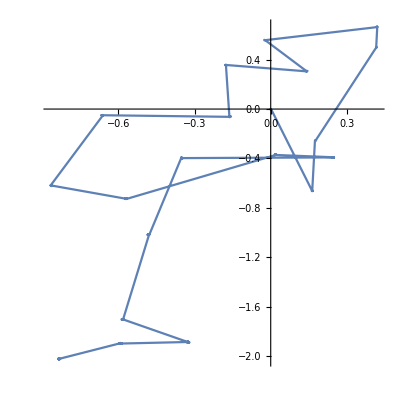

```mathematica
ListLinePlot[Trajs[[15]],AspectRatio->1,PlotRange->All]
```

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\CTRW\\trajs_cor_levy.dat"];
```

```mathematica
deltax=Map[Differences[#[[All,1]]]&,Trajs];
s=Map[MemberQ[#,0]&,deltax];
MemberQ[s,False]
MemberQ[s,True]
```

True

False

```mathematica
Correlated CTRW Cutoff
```

```mathematica
NTrajs=5000;
Trajs=Table[{0,0},{NTrajs},{len+1}];
```

```mathematica
T1=AbsoluteTime[]
For[i=1,i≤ NTrajs,i++,
alpha=RandomReal[{0.5,0.99}];
waitmax=50;

times={0};
t=0;
temptime=0;
While[t≤len,
waitting=(1-(1-(1+waitmax)^-alpha)*RandomReal[])^(-1/alpha);
t=t+waitting;
AppendTo[times,waitting];
];

Time=Accumulate[times];
Time[[-1]]=len;
step=Time+1;
If[Length[step]≤ 2,Print[i,"No jump"];i=i-1;Continue[];];

(*steplength=RandomReal[NormalDistribution[0,sigma],{Length[step-2],2}];*)
steplength=RandomVariate[RayleighDistribution[sigma],Length[step-2]];
stepjump=Table[{0,0},{Length[steplength]}];
For[k=1,k≤ Length[steplength],k++,
theta=RandomReal[{0,2*Pi}];
stepjump[[k,1]]=steplength[[k]]*Cos[theta];
stepjump[[k,2]]=steplength[[k]]*Sin[theta];
];

(*trajs=Accumulate[steplength];*)
trajs=Accumulate[stepjump];

trajs=Prepend[trajs,{0,0}];

For[j=1,j≤ Length[step]-1,j++,
waiting=Ceiling[step[[j]]];
jump=Floor[step[[j+1]]];
For[k=waiting,k≤ jump,k++,
Trajs[[i,k,1]]=trajs[[j,1]];
Trajs[[i,k,2]]=trajs[[j,2]];
]
]
]
T2=AbsoluteTime[]
T2-T1
```

3.918658790562×10^9

3.918658802531×10^9

11.969

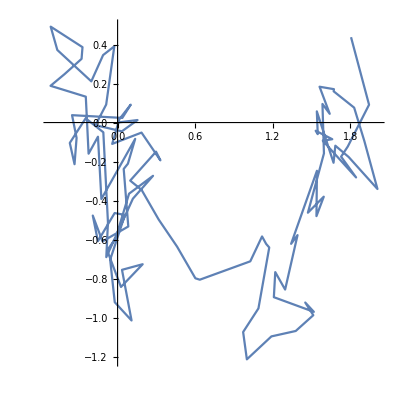

```mathematica
ListLinePlot[Trajs[[5000]],AspectRatio->1,PlotRange->All]
```

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\CTRW\\trajs_cut1.dat"];
```

```mathematica
NTrajs=5000;
Trajs=Table[{0,0},{NTrajs},{len+1}];
```

```mathematica
T1=AbsoluteTime[]
For[i=1,i≤ NTrajs,i++,
alpha=RandomReal[{0.5,0.99}];
waitmax=40;
times={0};
t=0;
event=0;

While[t≤len,
r=RandomReal[];
randwait=tau/.Solve[Exp[-tau/waitmax]/((1+tau)^alpha)==1-r,tau];
randwait=Flatten[randwait];
If[(Length[randwait]<1)||(randwait[[1]]<0),Print["no solution"];Continue[];];
waitting=randwait[[1]];
t=t+waitting;
AppendTo[times,waitting];
event=event+1;
If[event>1000,Print["Something is wrong"];Break[];];
];

Time=Accumulate[times];
Time[[-1]]=len;
step=Time+1;
If[Length[step]≤ 2,Print[i,"No jump"];i=i-1;Continue[];];

(*steplength=RandomReal[NormalDistribution[0,sigma],{Length[step-2],2}];*)
steplength=RandomVariate[RayleighDistribution[sigma],Length[step-2]];
stepjump=Table[{0,0},{Length[steplength]}];
For[k=1,k≤ Length[steplength],k++,
theta=RandomReal[{0,2*Pi}];
stepjump[[k,1]]=steplength[[k]]*Cos[theta];
stepjump[[k,2]]=steplength[[k]]*Sin[theta];
];

(*trajs=Accumulate[steplength];*)
trajs=Accumulate[stepjump];

trajs=Prepend[trajs,{0,0}];

For[j=1,j≤ Length[step]-1,j++,
waiting=Ceiling[step[[j]]];
jump=Floor[step[[j+1]]];
For[k=waiting,k≤ jump,k++,
Trajs[[i,k,1]]=trajs[[j,1]];
Trajs[[i,k,2]]=trajs[[j,2]];
]
];
If[Mod[i,200]==0,Print[i,"trajectory"]];
]
T2=AbsoluteTime[]
T2-T1
```

3.918661510905×10^9

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

200trajectory

400trajectory

600trajectory

800trajectory

1000trajectory

1200trajectory

1400trajectory

1600trajectory

1800trajectory

2000trajectory

2200trajectory

2400trajectory

2600trajectory

2800trajectory

3000trajectory

3200trajectory

3400trajectory

3600trajectory

3800trajectory

4000trajectory

4200trajectory

4400trajectory

4600trajectory

4800trajectory

5000trajectory

3.918662519064×10^9

1008.159

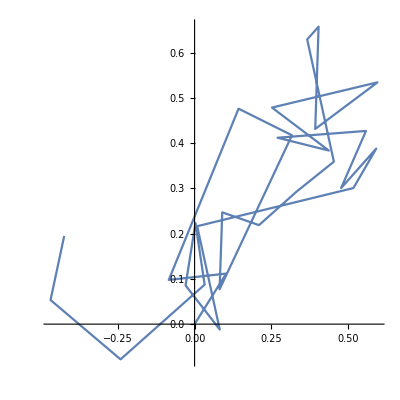

```mathematica
ListLinePlot[Trajs[[1]],AspectRatio->1,PlotRange->All]
```

```mathematica
Put[N[Trajs],"E:\\KG\\Trajs\\CTRW\\trajs_cut2.dat"];
```

```mathematica
times
```

{0,0.259651,11.3216,0.393477,2.50686,1.27656,4.0153,14.8655,9.31591,0.103186,0.651157,0.169677,1.47337,0.153962,0.558013,0.176427,0.744437,2.98559,0.28673,0.680272,0.633848,0.334114,0.389172,0.228828,0.303972,1.78391,0.174094,0.257869,3.29723,0.530782,0.162824,1.23101,0.53881,2.53178,1.73334,4.69448,0.826285,0.266157,1.83973,0.308659,0.627182,5.94726,0.428319,0.469798,2.00391,2.0801,1.3199,1.60013,0.0192743,1.21978,1.12708,1.84799,0.504002,0.602496,0.382374,0.696487,2.83909,0.467515,2.44469,0.297046,0.0108117,2.50452,1.82031,13.0111,8.69058,0.310133,0.282863,0.78123,0.256352,5.87832,0.912664,0.0421872,0.500423,16.9131,20.6162,1.29021,1.79533,3.27172,1.75208,4.60218,27.3075,8.12135,3.88695,0.283003,1.46223,0.4484,6.75315,0.160656,15.5513,2.76815,0.956173,0.647376,0.693034,0.374164,20.7483,0.198643,0.806121,1.05735,14.2097,6.47833,1.25999,0.24396,1.35226,0.34824,0.00734885,5.10559,4.29099,0.0420544,3.00596,0.0650473,2.35568,3.54897,0.0391611,0.322272,0.0438201,0.273885,1.79044,0.191053,15.6721,3.24967,0.24363,0.683901,0.817487,0.603828,1.23146,2.5163,0.481219,0.769777,0.204405,1.03492,0.807325,0.00466997,0.634603,0.117125,1.27452,3.21554,2.87656,0.349351,1.68968,2.77163,0.0426908,0.131593,0.279144,8.40702,0.119212,0.0247957,0.102882,0.193218,57.855,0.49238,1.20061,0.751509,0.111176,5.20986,2.678,0.0623759,0.0937553,4.0682,2.70569,0.601037,1.13928,1.19154,0.739675,0.324709,0.201701,0.572414,0.357621,5.9221,11.2951,1.26584,2.05563,2.17695,3.25574,13.6853,0.0795541,2.75618,0.933954,12.3374}

```mathematica
step
```

{1,1.25965,12.5812,12.9747,15.4815,16.7581,20.7734,35.6389,44.9548,45.058,45.7092,45.8789,47.3522,47.5062,48.0642,48.2406,48.9851,51.9707,52.2574,52.9377,53.5715,53.9056,54.2948,54.5236,54.8276,56.6115,56.7856,57.0435,60.3407,60.8715,61.0343,62.2653,62.8041,65.3359,67.0692,71.7637,72.59,72.8562,74.6959,75.0046,75.6317,81.579,82.0073,82.4771,84.481,86.5611,87.881,89.4812,89.5004,90.7202,91.8473,93.6953,94.1993,94.8018,95.1842,95.8807,98.7197,99.1873,101.632,101.929,101.94,104.444,106.265,119.276,127.966,128.276,128.559,129.341,129.597,135.475,136.388,136.43,136.93,153.844,174.46,175.75,177.545,180.817,182.569,187.171,214.479,222.6,226.487,226.77,228.232,228.681,235.434,235.595,251.146,253.914,254.87,255.518,256.211,256.585,277.333,277.532,278.338,279.395,293.605,300.083,301.343,301.587,302.939,303.288,303.295,308.401,312.692,312.734,315.74,315.805,318.16,321.709,321.748,322.071,322.115,322.388,324.179,324.37,340.042,343.292,343.535,344.219,345.037,345.64,346.872,349.388,349.869,350.639,350.844,351.879,352.686,352.691,353.325,353.442,354.717,357.932,360.809,361.158,362.848,365.62,365.662,365.794,366.073,374.48,374.599,374.624,374.727,374.92,432.775,433.267,434.468,435.22,435.331,440.541,443.219,443.281,443.375,447.443,450.149,450.75,451.889,453.081,453.82,454.145,454.347,454.919,455.277,461.199,472.494,473.76,475.815,477.992,481.248,494.933,495.013,497.769,498.703,501}

```mathematica
alpha
```

0.921608

```mathematica
Max[times]
```

54.836

```mathematica
Mean[times]
```

5.27517

```mathematica
randwait=tau/.Solve[Exp[-tau/waitmax]/((1+tau)^alpha)==1-r,tau]
If[Length[randwait]<1,Print["no solution"];Continue[];]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{0.227487}